```mathematica
(*Define Dirac Spinor, take electron pair annihilation and muon pair production as example*)
```

```mathematica
Quit[]
```

```mathematica
ClearAll[p1, p2, p3, p4];
```

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],F[2,{1}]}->{F[2,{2}],F[2,{1}]},InsertionLevel->{Classes},
ExcludeParticles->{S[_],V[2]}
];
```

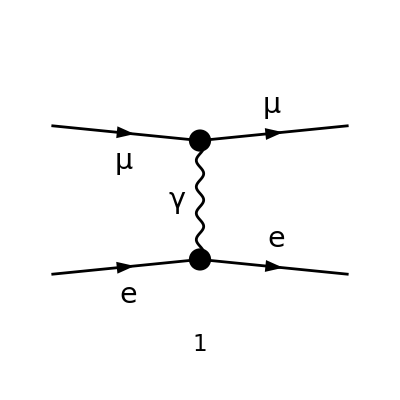

```mathematica
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{300,250}];
```

```mathematica
(*Creating amplitude*)
```

```mathematica
amp0 = FCFAConvert[CreateFeynAmp[diags], IncomingMomenta->{pm1, pe2}, OutgoingMomenta->{pm3, pe4},
UndoChiralSplittings->True, ChangeDimension->4,
SMP->True, List->False,Contract->True]
```

-(e^2 (φ(OverBar[pe4],m_e)).(γ̄)^Lor1.(φ(OverBar[pe2],m_e)) (φ(OverBar[pm3],m_μ)).(γ̄)^Lor1.(φ(OverBar[pm1],m_μ)))/(OverBar[pe4]-OverBar[pe2])^2

```mathematica
FCClearScalarProducts[];
```

```mathematica
SetMandelstam[s,t,u,pm1,pe2,-pm3,-pe4,SMP["m_mu"], SMP["m_e"], SMP["m_mu"], SMP["m_e"]]
```

(m_e^2 | m_e^2-t/2 | -m_e^2/2-m_μ^2/2+s/2 | m_e^2/2+m_μ^2/2-u/2 | m_e^2 | m_e^2/2+m_μ^2/2-u/2 | -m_e^2/2-m_μ^2/2+s/2 | m_μ^2 | m_μ^2-t/2 | m_μ^2 | m_e^2 | m_e^2-t/2 | -m_e^2/2-m_μ^2/2+s/2 | m_e^2/2+m_μ^2/2-u/2 | m_e^2 | m_e^2/2+m_μ^2/2-u/2 | -m_e^2/2-m_μ^2/2+s/2 | m_μ^2 | m_μ^2-t/2 | m_μ^2 | m_e^2 | m_e^2-t/2 | -m_e^2/2-m_μ^2/2+s/2 | m_e^2/2+m_μ^2/2-u/2 | m_e^2 | m_e^2/2+m_μ^2/2-u/2 | -m_e^2/2-m_μ^2/2+s/2 | m_μ^2 | m_μ^2-t/2 | m_μ^2 | m_e^2 | m_e^2-t/2 | -m_e^2/2-m_μ^2/2+s/2 | m_e^2/2+m_μ^2/2-u/2 | m_e^2 | m_e^2/2+m_μ^2/2-u/2 | -m_e^2/2-m_μ^2/2+s/2 | m_μ^2 | m_μ^2-t/2 | m_μ^2)

```mathematica
(*spin average for initial beam, and spin sum for final beam*)
```

```mathematica
ampSquared = (amp0 (ComplexConjugate[amp0]))//FeynAmpDenominatorExplicit//FermionSpinSum[#, ExtraFactor->1/4]& //DiracSimplify//Simplify
```

(2 e^4 (-2 m_e^2 (-2 m_μ^2+s-t+u)+2 m_e^4+2 m_μ^4-2 m_μ^2 (s-t+u)+s^2+u^2))/t^2

```mathematica
(*Dirac Gamma Matrices*)
```

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
```

```mathematica
metric = {{1 ,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
GMatrix[1]= gamma0;
GMatrix[2]= gamma1;
GMatrix[3]= gamma2;
GMatrix[4]= gamma3;
```

```mathematica
E1 = 160.0; m=0.00051;Mmu = 0.105;
```

```mathematica
E4 = E1+m-E3;
```

```mathematica
p1 = {E1,0,0,√(E1^2-Mmu^2)}(*incoming muon*) 
p2={m, 0,0,0} (*electron at rest*)
p3 = {E3, √(E3^2-Mmu^2)*Sin[Subscript[θ, 1]], 0,√(E3^2-Mmu^2)*Cos[Subscript[θ, 1]]}(*outgoing muon*)
p4={E4 ,-√(E4^2-m)*Sin[Subscript[θ, 2]], 0,-√(E4^2-m^2)*Cos[Subscript[θ, 2]]}(* outgoing electron*)
```

{160.,0,0,160.}

{0.00051,0,0,0}

{E3,√(E3^2-0.011025) sin(θ_1),0,√(E3^2-0.011025) cos(θ_1)}

{160.001-E3,-√((160.001-E3)^2-0.00051) sin(θ_2),0,-√((160.001-E3)^2-2.601×10^-7) cos(θ_2)}

```mathematica
-Graphics--Graphics-
```

```mathematica
mandelStamS = (p1+p2).metric.(p1+p2)//Simplify
mandelStamT = (p4-p2).metric.(p4-p2)//Simplify
mandelStamU = (p3-p2).metric.(p3-p2)//Simplify
```

0.174225

0.00102 E3-0.00025487 cos(2 θ_2)-0.162945

0.0110253-0.00102 E3

```mathematica
normalAmp = ampSquared/.{t->mandelStamT,s->mandelStamS, u->mandelStamU,SMP["e"]^4->(16 π^2 α^2), SMP["m_mu"]->Mmu, SMP["m_e"]->m}//Simplify
```

(315.827 α^2 (1. E3^2+21.6182 E3-5.40178 cos(2 θ_2)+22146.5))/(-1. E3+0.249873 cos(2 θ_2)+159.75)^2

```mathematica
$Assumptions={Ε∈Reals,m∈Reals, Subscript[p, xyz]∈Reals, Subscript[θ, 1]∈Reals, Subscript[θ, 2]∈Reals, ϕ∈Reals, E3∈Reals};
```

```mathematica
(*
1. initial electron and positron spinors.
2. Final muon and anti-muon spinors 
3. Gamma matrices
4. 1 stannds for positve helicity, "+", -1 stands for "-" helicity.
*)
```

```mathematica
spinorU[θ_, ϕ_,s_]:=Module[{Ν =Sqrt[ Ε+m]},
If[s==1,
{{Ν*Cos[θ/2]},
{Ν*Exp[ⅈ ϕ]Sin[θ/2]},
{(Subscript[p, xyz]/Ν)Cos[θ/2]},
{(Subscript[p, xyz]/Ν)Sin[θ/2]Exp[ⅈ ϕ]}
},
{{-Ν*Sin[θ/2]},
{Ν*Exp[ⅈ ϕ]Cos[θ/2]},
{(Subscript[p, xyz]/Ν)Sin[θ/2]},
{-(Subscript[p, xyz]/Ν)Cos[θ/2]Exp[ⅈ ϕ]}
}
]
];
```

```mathematica
spinorV[θ_, ϕ_,s_]:=Module[{Ν =Sqrt[ Ε+m]},
If[s==1,
{{(Subscript[p, xyz]/Ν)Sin[θ/2]},
{-(Subscript[p, xyz]/Ν)Cos[θ/2]Exp[ⅈ ϕ]},
{-Ν*Sin[θ/2]},
{Ν*Cos[θ/2]*Exp[ⅈ ϕ]}
},
{{(Subscript[p, xyz]/Ν)Cos[θ/2]},
{(Subscript[p, xyz]/Ν)Sin[θ/2]Exp[ⅈ ϕ]},
{Ν*Cos[θ/2]},
{Ν*Sin[θ/2]*Exp[ⅈ ϕ]}
}
]
];
```

incoming muon, P1,  spinors, θ = 0, ϕ=0;

```mathematica
up1up = spinorU[0, 0, 1]/.{m->Mmu, Subscript[p, xyz]->√(E1^2-Mmu^2), Ε->E1}//Simplify
up1down = spinorU[0, 0, -1]/.{m->Mmu, Subscript[p, xyz]->√(E1^2-Mmu^2), Ε->E1}//Simplify
```

(12.6533
0
12.645
0)

(0
12.6533
0
-12.645)

electron at (rest), P2,  spinor definition, θ = 0, ϕ = 0;

```mathematica
up2up = spinorU[0, 0, 1]/.{m->m, Subscript[p, xyz]->0,Ε->m}
up2down = spinorU[0,0,-1]/.{m->m, Subscript[p, xyz]->0, Ε->m}
```

(0.0319374
0
0.
0)

(0
0.0319374
0
0.)

Outgoing muon, p3,  spinors, θ = θ_1, ϕ = 0;

```mathematica
up3up = spinorU[Subscript[θ, 1], 0, 1]/.{m->Mmu,Ε->E3, Subscript[p, xyz]->√(E3^2-Mmu^2)}//Simplify
up3down = spinorU[Subscript[θ, 1], 0, -1]/.{m->Mmu, Ε->E3,Subscript[p, xyz]->√(E3^2-Mmu^2)}//Simplify
```

(√(E3+0.105) cos(θ_1/2)
√(E3+0.105) sin(θ_1/2)
(√(E3^2-0.011025) cos(θ_1/2))/(√(E3+0.105))
(√(E3^2-0.011025) sin(θ_1/2))/(√(E3+0.105)))

(-√(E3+0.105) sin(θ_1/2)
√(E3+0.105) cos(θ_1/2)
(√(E3^2-0.011025) sin(θ_1/2))/(√(E3+0.105))
-(√(E3^2-0.011025) cos(θ_1/2))/(√(E3+0.105)))

Outgoing electron , p4, spinors, θ = θ_2, ϕ = 0;

```mathematica
up4up = spinorU[Subscript[θ, 2], π, 1]/.{m->m, Subscript[p, xyz]->√(E4^2-m^2), Ε->E4}//Simplify
up4down = spinorU[Subscript[θ, 2], π, -1]/.{m->m, Subscript[p, xyz]->√(E4^2-m^2), Ε->E4}//Simplify
```

(√(160.001-E3) cos(θ_2/2)
-√(160.001-E3) sin(θ_2/2)
(√(E3^2-320.001 E3+25600.2) cos(θ_2/2))/(√(160.001-1. E3))
-(√(E3^2-320.001 E3+25600.2) sin(θ_2/2))/(√(160.001-1. E3)))

(-√(160.001-E3) sin(θ_2/2)
-√(160.001-E3) cos(θ_2/2)
(√(E3^2-320.001 E3+25600.2) sin(θ_2/2))/(√(160.001-1. E3))
(√(E3^2-320.001 E3+25600.2) cos(θ_2/2))/(√(160.001-1. E3)))

for e mu > e mu scattering, we have 4*4 matrix elements:
RR→RR	RR→RL	RR→LR	 RR→LL
RL→RR	RL→RL	RL→LR	 RL→LL
LR→RR	LR→RL	LR→LR	 LR→LL
LL→RR	LL→RL	LL→LR	 LL→LL

```mathematica
(*First row*)
```

```mathematica
maRRRR=
(Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4up] .gamma0.GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maRRRL = (Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4down] .gamma0.GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maRRLR =(Flatten[Table[Transpose[up3down].gamma0 .GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0.GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maRRLL = (Flatten[Table[Transpose[up3down].gamma0 .GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4down].gamma0 .GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
(*second Row*)
```

```mathematica
maRLRR = (Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maRLRL = (Flatten[Table[Transpose[up3up].gamma0 .GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4down].gamma0.GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maRLLR = (Flatten[Table[Transpose[up3down].gamma0 .GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maRLLL = (Flatten[Table[Transpose[up3down] .gamma0.GMatrix[i].up1up,{i, 4}]].metric.
Flatten[Table[Transpose[up4down].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
(*3- Row*)
```

```mathematica
maLRRR =  (Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0 .GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maLRRL=  (Flatten[Table[Transpose[up3up].gamma0 .GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4down] .gamma0.GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maLRLR= (Flatten[Table[Transpose[up3down].gamma0 .GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0 .GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
maLRLL=  (Flatten[Table[Transpose[up3down].gamma0 .GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4down] .gamma0.GMatrix[i].up2up,{i, 4}]])//Simplify;
```

```mathematica
(*4-row*)
```

```mathematica
maLLRR=  (Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4up].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maLLRL=(Flatten[Table[Transpose[up3up] .gamma0.GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4down].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maLLLR=(Flatten[Table[Transpose[up3down] .gamma0.GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4up] .gamma0.GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
maLLLL=(Flatten[Table[Transpose[up3down] .gamma0.GMatrix[i].up1down,{i, 4}]].metric.
Flatten[Table[Transpose[up4down].gamma0 .GMatrix[i].up2down,{i, 4}]])//Simplify;
```

```mathematica
factor = 4π*α/mandelStamT
```

(4 π α)/(0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)

```mathematica
scatElmassive={
factor*{maRRRR, maRRRL, maRRLR, maRRLL},
factor*{maRLRR, maRLRL,maRLLR, maRLLL},
factor*{maLRRR,maLRRL, maLRLR, maLRLL},
factor*{maLLRR, maLLRL, maLLLR, maLLLL}
}//Simplify
```

((4978.66 α (0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)-0.999344 √(E3^2-320.001 E3+25600.2) E3-0.104931 √(E3^2-320.001 E3+25600.2)-1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | -(4978.66 α (0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)+0.999344 √(E3^2-320.001 E3+25600.2) E3+0.104931 √(E3^2-320.001 E3+25600.2)+1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | -(4978.66 α (-0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)-0.999344 √(E3^2-320.001 E3+25600.2) E3-0.104931 √(E3^2-320.001 E3+25600.2)+1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | (4978.66 α (-0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)+0.999344 √(E3^2-320.001 E3+25600.2) E3+0.104931 √(E3^2-320.001 E3+25600.2)-1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75))
(4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))-0.404113 E3 √(160.001-E3) √(160.001-1. E3)-0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)-0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)-0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))-0.404113 E3 √(160.001-E3) √(160.001-1. E3)-0.0424318 √(160.001-E3) √(160.001-1. E3)+0.403848 √(E3^2-320.001 E3+25600.2) E3+0.042404 √(E3^2-320.001 E3+25600.2)+0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)-0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+0.404113 E3 √(160.001-E3) √(160.001-1. E3)+0.0424318 √(160.001-E3) √(160.001-1. E3)+0.403848 √(E3^2-320.001 E3+25600.2) E3+0.042404 √(E3^2-320.001 E3+25600.2)-0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)+0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+0.404113 E3 √(160.001-E3) √(160.001-1. E3)+0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)+0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)+0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945))
(4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+0.404113 E3 √(160.001-E3) √(160.001-1. E3)+0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)+0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)+0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))-0.404113 E3 √(160.001-E3) √(160.001-1. E3)-0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)+0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2)+(0.807695 √(E3^2-320.001 E3+25600.2) E3+0.084808 √(E3^2-320.001 E3+25600.2)-0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+0.404113 E3 √(160.001-E3) √(160.001-1. E3)+0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)-0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2)+(0.807695 √(E3^2-320.001 E3+25600.2) E3+0.084808 √(E3^2-320.001 E3+25600.2)+0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945)) | (4 π α ((-0.403848 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))-0.404113 E3 √(160.001-E3) √(160.001-1. E3)-0.0424318 √(160.001-E3) √(160.001-1. E3)-0.403848 √(E3^2-320.001 E3+25600.2) E3-0.042404 √(E3^2-320.001 E3+25600.2)-0.404113 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2)+(-0.807695 √(E3^2-320.001 E3+25600.2) E3-0.084808 √(E3^2-320.001 E3+25600.2)-0.808225 √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2)))/(√((E3+0.105) (160.001-1. E3)) (0.00102 E3-0.00025487 cos(2 θ_2)-0.162945))
-(4978.66 α (-0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)+0.999344 √(E3^2-320.001 E3+25600.2) E3+0.104931 √(E3^2-320.001 E3+25600.2)-1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) sin(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | -(4978.66 α (-0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)-0.999344 √(E3^2-320.001 E3+25600.2) E3-0.104931 √(E3^2-320.001 E3+25600.2)+1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_1/2) cos(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | -(4978.66 α (0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)+0.999344 √(E3^2-320.001 E3+25600.2) E3+0.104931 √(E3^2-320.001 E3+25600.2)+1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) sin(θ_2/2) cos(θ_1/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)) | -(4978.66 α (0.999344 √(160.001-E3) √((E3^2-0.011025) (160.001-1. E3))+1. E3 √(160.001-E3) √(160.001-1. E3)+0.105 √(160.001-E3) √(160.001-1. E3)-0.999344 √(E3^2-320.001 E3+25600.2) E3-0.104931 √(E3^2-320.001 E3+25600.2)-1. √((E3^2-0.011025) (E3^2-320.001 E3+25600.2))) cos(θ_1/2) cos(θ_2/2))/(√((E3+0.105) (160.001-1. E3)) (1. E3-0.249873 cos(2 θ_2)-159.75)))

```mathematica
(*fm-RR, RL, LR, LL represents amplitude for final e and muon*)
```

```mathematica
fmRR =Mean[Table[scatElmassive[[i, 1]] , {i, 4}]]//Simplify;
fmRL = Mean[Table[scatElmassive[[i, 2]] , {i, 4}]]//Simplify;
fmLR = Mean[Table[scatElmassive[[i, 3]] , {i, 4}]]//Simplify;
fmLL = Mean[Table[scatElmassive[[i, 4]] , {i, 4}]]//Simplify;
```

```mathematica
spinAveragedMatrix = {
fmRR/.{α->0.0073}, 
fmRL/.{α->0.0073}, 
fmLR/.{α->0.0073}, 
fmLL/.{α->0.0073}
}//Simplify//Chop[#, 10^-7]&;
```

```mathematica
normFactor=Sum[spinAveragedMatrix[[i]]^2,{i, 4}]//Simplify//Chop[#, 10^-6]&;
```

```mathematica
(*normFactor=normalAmp/.{α->0.0073}//Simplify*)
```

```mathematica
rho2=(KroneckerProduct[spinAveragedMatrix,Transpose[spinAveragedMatrix]]/normFactor)//Chop[#, 10^-7]&
```

(1)
 |  |  |  |

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DumpSave["DesnityMatrix_160GeV.mx",rho2];
```

```mathematica
dumrho = rho2/.{E3->0.99, Subscript[θ, 1]->0.001, Subscript[θ, 2]->0.1}
```

(0.174038 | -0.00905005 | 0.336656 | 0.174154
-0.00905005 | 0.000470607 | -0.0175063 | -0.00905608
0.336656 | -0.0175063 | 0.651222 | 0.33688
0.174154 | -0.00905608 | 0.33688 | 0.17427)

```mathematica
Tr[dumrho]
```

1.

```mathematica
partialRho = ArrayFlatten[ Table[Partition[rho2, {2,2}][[i, j]]//Transpose,{i,2},{j,2}]]
```

(-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))) (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851))
-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851))
-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))) (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851))
-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)))

```mathematica
rhoTr2Reduced = {{partialRho[[1,1]],partialRho[[1,4]]},{partialRho[[4,1]],partialRho[[4,4]]}}
```

(-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))-2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))-0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1+θ_2))+0.0785738 sin(1/2 (θ_1+θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851))
-(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (-0.747545 E3^2 sin(1/2 (θ_1-θ_2))+0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))-0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))-0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))+0.66983 E3 sin(1/2 (θ_1-θ_2))+0.0785738 sin(1/2 (θ_1-θ_2))) (0.747545 E3^2 sin(1/2 (θ_1-θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1+θ_2))+0.672771 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1+θ_2))-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1+θ_2))+0.070641 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1+θ_2))+(E3 (-0.672771 √(E3^2-0.011025)-2.01831 √(E3^2-2.00104 E3+1.00104))+0.673471 √(E3^2-0.011025)-0.211923 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1-θ_2))+(-0.747545 E3^2+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1-θ_2))-0.0785738 sin(1/2 (θ_1-θ_2))))/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)) | -(1. (-1. E3+0.24987 cos(2 θ_2)+0.75013)^2 (0.747545 E3^2 sin(1/2 (θ_1+θ_2))-0.672771 √(E3^2-0.011025) E3 sin(1/2 (θ_1-θ_2))+2.01831 √(E3^2-2.00104 E3+1.00104) E3 sin(1/2 (θ_1-θ_2))+0.673471 √(E3^2-0.011025) sin(1/2 (θ_1-θ_2))+0.211923 √(E3^2-2.00104 E3+1.00104) sin(1/2 (θ_1-θ_2))+0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104)) sin(1/2 (θ_1+θ_2))+(-0.747545 E3^2-0.747545 √((E3^2-0.011025) (E3^2-2.00104 E3+1.00104))+0.66983 E3+0.0785738) cos(1/2 (θ_1-θ_2))+(-0.672771 √(E3^2-0.011025) E3-0.672771 √(E3^2-2.00104 E3+1.00104) E3+0.673471 √(E3^2-0.011025)-0.070641 √(E3^2-2.00104 E3+1.00104)) cos(1/2 (θ_1+θ_2))-0.66983 E3 sin(1/2 (θ_1+θ_2))-0.0785738 sin(1/2 (θ_1+θ_2)))^2)/((E3-1.00104) (E3+0.105) (1. E3-0.24987 cos(2 θ_2)-0.75013)^2 (0.0168304 E3^2+0.356846 E3-0.0891652 cos(2 θ_2)-0.250851)))

```mathematica
Dimensions[rhoTr2Reduced]
```

{2,2}

```mathematica
(*Integrating over electron angle: Subscript[θ, 2]*)
```

```mathematica
rhoCdet =Integrate[ Det[rhoTr2Reduced],{Subscript[θ, 2], 0, π/3}];
```

$Aborted

```mathematica
xTicks = SetPrecision[Table[i*π,{i,  0.,1, 0.1}],2];
yTicks={0, π/6,π/3, π/2, 2π/3, π};
eTicks = Table[i, {i, 0, 1.01, 0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

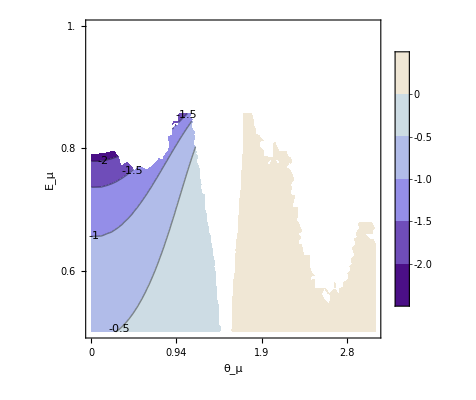

```mathematica
ContourPlot[rhoCdet,{Subscript[θ, 1], 0, π},{Subscript[Ε, 3], 0.5,0.9999 },PlotLegends->Automatic, 
FrameLabel->{Style["θ_μ",FontSize->14,Blue],Style["Ε_μ",FontSize->14,Red]}
,LabelStyle->Directive[Black,Bold],FrameTicks->{xTicks,eTicks},PlotTheme->"Classic",ContourLabels->True]
```

```mathematica
Emu//Max
```

0.999018

```mathematica
rho2NoE3 = rho2/.{E3->0.98};
```

```mathematica
rho2ParTransposeE3 = ArrayFlatten[ Table[Partition[rho2NoE3, {2,2}][[i, j]]//Transpose,{i,2},{j,2}]]
```

((43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2)))
(43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2)))
(43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2)))
(43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))))

```mathematica
rho2CNoE3 =  {{rho2ParTransposeE3[[1,1]],rho2ParTransposeE3[[1,4]]},{rho2ParTransposeE3[[4,1]],rho2ParTransposeE3[[4,4]]}}
```

((43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (-0.0587139 sin(1/2 (θ_1-θ_2))+0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2)))
(43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0320067 sin(1/2 (θ_1-θ_2))-0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))) (-0.0320067 sin(1/2 (θ_1-θ_2))+0.0287661 sin(1/2 (θ_1+θ_2))-0.0311296 cos(1/2 (θ_1-θ_2))+0.0320067 cos(1/2 (θ_1+θ_2))))/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))) | (43.8051 (0.24987 cos(2 θ_2)-0.22987)^2 (0.0587139 sin(1/2 (θ_1-θ_2))-0.00212376 sin(1/2 (θ_1+θ_2))+0.00212376 cos(1/2 (θ_1-θ_2))-0.00118175 cos(1/2 (θ_1+θ_2)))^2)/((0.22987-0.24987 cos(2 θ_2))^2 (0.115023-0.0891652 cos(2 θ_2))))

```mathematica
detrhoCNoE3 = Det[rho2CNoE3]//Chop[#, 10^-6]&
```

-(7.02407×10^-6 cos^4(2 θ_2) cos^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000258474 cos^3(2 θ_2) cos^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000356678 cos^2(2 θ_2) cos^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000218753 cos(2 θ_2) cos^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(5.03108×10^-6 cos^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000288882 cos^4(2 θ_2) cos(1/2 (θ_1+θ_2)) cos^3(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000106304 cos^3(2 θ_2) cos(1/2 (θ_1+θ_2)) cos^3(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000146693 cos^2(2 θ_2) cos(1/2 (θ_1+θ_2)) cos^3(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000899675 cos(2 θ_2) cos(1/2 (θ_1+θ_2)) cos^3(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000206916 cos(1/2 (θ_1+θ_2)) cos^3(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000445536 cos^4(2 θ_2) cos^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.00016395 cos^3(2 θ_2) cos^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000226241 cos^2(2 θ_2) cos^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000138755 cos(2 θ_2) cos^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000319121 cos^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000146187 cos^4(2 θ_2) sin^2(1/2 (θ_1-θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000537944 cos^3(2 θ_2) sin^2(1/2 (θ_1-θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000742329 cos^2(2 θ_2) sin^2(1/2 (θ_1-θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000455274 cos(2 θ_2) sin^2(1/2 (θ_1-θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000104708 sin^2(1/2 (θ_1-θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000119959 cos^4(2 θ_2) sin^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000441428 cos^3(2 θ_2) sin^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000609143 cos^2(2 θ_2) sin^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000373591 cos(2 θ_2) sin^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(8.5922×10^-6 sin^2(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000266784 cos^4(2 θ_2) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000981721 cos^3(2 θ_2) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000135471 cos^2(2 θ_2) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000830853 cos(2 θ_2) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000191088 sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000305395 cos^4(2 θ_2) cos^3(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.00011238 cos^3(2 θ_2) cos^3(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000155078 cos^2(2 θ_2) cos^3(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.00009511 cos(2 θ_2) cos^3(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000218743 cos^3(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000302807 cos^4(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000111428 cos^3(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000153764 cos^2(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000943041 cos(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000021689 cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000246681 cos^4(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000907744 cos^3(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000125263 cos^2(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000768245 cos(2 θ_2) cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000176688 cos(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000548762 cos^4(2 θ_2) cos(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000201935 cos^3(2 θ_2) cos(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000278658 cos^2(2 θ_2) cos(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000170902 cos(2 θ_2) cos(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000393058 cos(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)) cos(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(7.85002×10^-6 cos^4(2 θ_2) cos^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000288868 cos^3(2 θ_2) cos^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000398619 cos^2(2 θ_2) cos^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000244475 cos(2 θ_2) cos^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(5.62268×10^-6 cos^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000810432 cos^4(2 θ_2) sin^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000298226 cos^3(2 θ_2) sin^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000411533 cos^2(2 θ_2) sin^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000252395 cos(2 θ_2) sin^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000580483 sin^4(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(5.1217×10^-6 cos^4(2 θ_2) sin^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000018847 cos^3(2 θ_2) sin^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000260077 cos^2(2 θ_2) sin^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000159507 cos(2 θ_2) sin^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(3.66849×10^-6 sin^4(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000227786 cos^4(2 θ_2) sin(1/2 (θ_1-θ_2)) sin^3(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000838216 cos^3(2 θ_2) sin(1/2 (θ_1-θ_2)) sin^3(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000115669 cos^2(2 θ_2) sin(1/2 (θ_1-θ_2)) sin^3(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000709402 cos(2 θ_2) sin(1/2 (θ_1-θ_2)) sin^3(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000163155 sin(1/2 (θ_1-θ_2)) sin^3(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000015628 cos^4(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000575086 cos^3(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000793583 cos^2(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000486709 cos(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000111938 cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1-θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000126817 cos^4(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000466664 cos^3(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000643967 cos^2(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000394949 cos(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(9.08341×10^-6 cos^2(1/2 (θ_1+θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000373474 cos^4(2 θ_2) sin^2(1/2 (θ_1-θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000137432 cos^3(2 θ_2) sin^2(1/2 (θ_1-θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000189648 cos^2(2 θ_2) sin^2(1/2 (θ_1-θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000116312 cos(2 θ_2) sin^2(1/2 (θ_1-θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000267506 sin^2(1/2 (θ_1-θ_2)) sin^2(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000153593 cos^4(2 θ_2) sin^3(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000565198 cos^3(2 θ_2) sin^3(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000779937 cos^2(2 θ_2) sin^3(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000047834 cos(2 θ_2) sin^3(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000110013 sin^3(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000282157 cos^4(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.000103829 cos^3(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.000143277 cos^2(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)+(0.0000878729 cos(2 θ_2) cos^2(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)-(0.0000202098 cos^2(1/2 (θ_1+θ_2)) sin(1/2 (θ_1-θ_2)) sin(1/2 (θ_1+θ_2)))/((0.22987-0.24987 cos(2 θ_2))^4 (0.115023-0.0891652 cos(2 θ_2))^2)

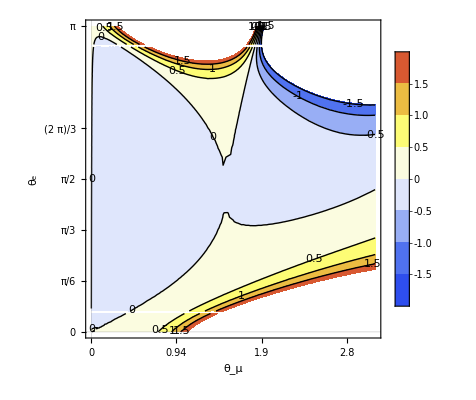

```mathematica
ContourPlot[detrhoCNoE3,{Subscript[θ, 1], 0,π},{Subscript[θ, 2], 0, π},PlotLegends->Automatic, 
FrameLabel->{Style["θ_μ",FontSize->14,Blue],Style["θ_e",FontSize->14,Red]}
,LabelStyle->Directive[Black,Bold],FrameTicks->{xTicks,yTicks},PlotTheme->"Scientific",ColorFunction->"TemperatureMap",ContourLabels->True]
```

```mathematica
(*two-qubit density matrix*)
```

```mathematica
π/3.
```

1.0472

```mathematica
Alep = {Subscript[SuperPlus[B], 1], Subscript[SuperPlus[B], 2], Subscript[SuperPlus[B], 3]}
Blep = {Subscript[SuperMinus[B], 1], Subscript[SuperMinus[B], 2], Subscript[SuperMinus[B], 3]}
```

{(B^+)_1,(B^+)_2,(B^+)_3}

{(B^-)_1,(B^-)_2,(B^-)_3}

```mathematica
Cmat = {{C11, C12, C13},{C21, C22, C23},{C31, C32, C33}}
```

(C11 | C12 | C13
C21 | C22 | C23
C31 | C32 | C33)

```mathematica
rho2qbuit = (IdentityMatrix[4]+
Sum[Alep[[i]]*KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]],{i, 3}]+
Sum[Blep[[j]]*KroneckerProduct[IdentityMatrix[2],PauliMatrix[j]],{j, 3}]+
Sum[Cmat[[i, j]]*KroneckerProduct[PauliMatrix[i], PauliMatrix[j]],{i,3},{j, 3}]
)
```

((B^-)_3+(B^+)_3+C33+1 | (B^-)_1-ⅈ (B^-)_2+C31-ⅈ C32 | (B^+)_1-ⅈ (B^+)_2+C13-ⅈ C23 | C11-ⅈ C12-ⅈ C21-C22
(B^-)_1+ⅈ (B^-)_2+C31+ⅈ C32 | -(B^-)_3+(B^+)_3-C33+1 | C11+ⅈ C12-ⅈ C21+C22 | (B^+)_1-ⅈ (B^+)_2-C13+ⅈ C23
(B^+)_1+ⅈ (B^+)_2+C13+ⅈ C23 | C11-ⅈ C12+ⅈ C21+C22 | (B^-)_3-(B^+)_3-C33+1 | (B^-)_1-ⅈ (B^-)_2-C31+ⅈ C32
C11+ⅈ C12+ⅈ C21-C22 | (B^+)_1+ⅈ (B^+)_2-C13-ⅈ C23 | (B^-)_1+ⅈ (B^-)_2-C31-ⅈ C32 | -(B^-)_3-(B^+)_3+C33+1)

```mathematica
Bplus = Table[Tr[rho2.KroneckerProduct[PauliMatrix[i], IdentityMatrix[2]]],{i, 3}]//Simplify//Chop;
```

```mathematica
Bminus = Table[Tr[rho2.KroneckerProduct[IdentityMatrix[2], PauliMatrix[i]]],{i, 3}]//Simplify//Chop;
```

```mathematica
Cmatrix= Table[Tr[rho2.KroneckerProduct[PauliMatrix[i], PauliMatrix[j]]],{i, 3},{j, 3}]//Simplify//Chop
```

((-5.3695 √((Ε_3-1.00102) (Ε_3-1.)) cos(θ_1)+0.0261316 √(Ε_3^2-0.011025) cos(θ_2)+Ε_3^4 (-437.867 sin(θ_1) sin(θ_2)-927.104 cos(θ_1) cos(θ_2))+Ε_3^3 (cos(θ_1) (486.532 √(Ε_3^2-2.00102 Ε_3+1.00102)+1712.08 cos(θ_2))+784.229 sin(θ_1) sin(θ_2))+Ε_3^2 (-0.248618 √(Ε_3^2-0.011025) cos(θ_2)+cos(θ_1) (-384.858 √(Ε_3^2-2.00102 Ε_3+1.00102)-646.31 cos(θ_2))-437.867 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102)-259.144 sin(θ_1) sin(θ_2))+Ε_3 (0.222767 √(Ε_3^2-0.011025) cos(θ_2)+cos(θ_1) (-96.9122 √(Ε_3^2-2.00102 Ε_3+1.00102)-133.837 cos(θ_2))+392.338 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102)-82.3861 sin(θ_1) sin(θ_2))+46.023 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)-4.83256 cos(θ_1-θ_2)-0.000144851 cos(θ_1+θ_2))/((Ε_3-1.00102) (Ε_3+0.105) (1. Ε_3^2+21.5759 Ε_3-20.5814)) | 0 | (-437.867 Ε_3^6 sin(θ_1-θ_2)+Ε_3^4 (-1409.26 √((Ε_3-1.00102) (Ε_3-1.)) sin(θ_1)-1896.04 √(Ε_3^2-0.011025) sin(θ_2)-2276.24 sin(θ_1-θ_2)+10.1479 sin(θ_1+θ_2))+Ε_3^3 (1307.75 √((Ε_3-1.00102) (Ε_3-1.)) sin(θ_1)+2717.73 √(Ε_3^2-0.011025) sin(θ_2)+1235.39 sin(θ_1-θ_2)-14.7288 sin(θ_1+θ_2))+51.1904 √(Ε_3^2-0.011025) sin(θ_2)+Ε_3^5 (486.532 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)+486.532 √(Ε_3^2-0.011025) sin(θ_2)+1660.19 sin(θ_1) cos(θ_2)-1665.33 sin(θ_2) cos(θ_1))+Ε_3^2 (-333.864 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)-1642.29 √(Ε_3^2-0.011025) sin(θ_2)-99.2943 sin(θ_1) cos(θ_2)+117.33 sin(θ_2) cos(θ_1))+Ε_3 (-51.1642 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)+282.871 √(Ε_3^2-0.011025) sin(θ_2)-72.7609 sin(θ_1) cos(θ_2)+69.5987 sin(θ_2) cos(θ_1))-4.83489 sin(θ_1) cos(θ_2)+4.26738 sin(θ_2) cos(θ_1))/((Ε_3-1.00102) (Ε_3+0.105) (1. Ε_3^2+21.5759 Ε_3-20.5814) (1.00026-1. Ε_3)^2)
0 | (Ε_3^3 (784.229-486.532 √(Ε_3^2-0.011025) cos(θ_1))-5.3695 √((Ε_3-1.00102) (Ε_3-1.)) cos(θ_2)-51.1381 √(Ε_3^2-0.011025) cos(θ_1)+20.3118 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025) cos(θ_1-θ_2)-25.7112 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025) cos(θ_1+θ_2)+Ε_3^2 (-437.867 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1) sin(θ_2)+51.0859 √(Ε_3^2-2.00102 Ε_3+1.00102) cos(θ_2)+cos(θ_1) (51.3699 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102) cos(θ_2)+922.476 √(Ε_3^2-0.011025))-259.144)+Ε_3 (392.338 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1) sin(θ_2)-45.7741 √(Ε_3^2-2.00102 Ε_3+1.00102) cos(θ_2)+cos(θ_1) (-46.0285 √(Ε_3^2-0.011025) √(Ε_3^2-2.00102 Ε_3+1.00102) cos(θ_2)-384.806 √(Ε_3^2-0.011025))-82.3861)-437.867 Ε_3^4-4.83242)/((Ε_3-1.00102) (Ε_3+0.105) (1. Ε_3^2+21.5759 Ε_3-20.5814)) | 0
(-437.867 Ε_3^6 sin(θ_1-θ_2)+Ε_3^4 (-1358.17 √((Ε_3-1.00102) (Ε_3-1.)) sin(θ_1)-1895.79 √(Ε_3^2-0.011025) sin(θ_2)-2166.04 sin(θ_1-θ_2)+100.057 sin(θ_1+θ_2))+Ε_3 (-86.22 √((Ε_3-1.00102) (Ε_3-1.)) sin(θ_1)+282.7 √(Ε_3^2-0.011025) sin(θ_2)-87.6956 sin(θ_1-θ_2)-14.9346 sin(θ_1+θ_2))+51.1642 √(Ε_3^2-0.011025) sin(θ_2)-5.37225 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)+Ε_3^5 (486.532 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)+486.532 √(Ε_3^2-0.011025) sin(θ_2)+1608.84 sin(θ_1) cos(θ_2)-1660.19 sin(θ_2) cos(θ_1))+Ε_3^3 (1159.78 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)+2717.01 √(Ε_3^2-0.011025) sin(θ_2)+933.787 sin(θ_1) cos(θ_2)-1220.66 sin(θ_2) cos(θ_1))+Ε_3^2 (-196.55 √(Ε_3^2-2.00102 Ε_3+1.00102) sin(θ_1)-1641.62 √(Ε_3^2-0.011025) sin(θ_2)+74.0862 sin(θ_1) cos(θ_2)+99.2943 sin(θ_2) cos(θ_1))-10.2398 sin(θ_1) cos(θ_2)+4.83489 sin(θ_2) cos(θ_1))/((Ε_3-1.00102) (Ε_3+0.105) (1. Ε_3^2+21.5759 Ε_3-20.5814) (1.00026-1. Ε_3)^2) | 0 | (Ε_3^3 (147.972 √((Ε_3-1.00102) (Ε_3-1.)) cos(θ_1)+2717.01 √(Ε_3^2-0.011025) cos(θ_2)+148.795 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)-1134. cos(θ_1-θ_2)-86.6612 cos(θ_1+θ_2))+cos(θ_1) (5.37225 √((Ε_3-1.00102) (Ε_3-1.))+4.83489 cos(θ_2))+51.1642 √(Ε_3^2-0.011025) cos(θ_2)+Ε_3^6 (386.497 sin(θ_1) sin(θ_2)+437.867 cos(θ_1) cos(θ_2))+Ε_3^5 (486.532 √(Ε_3^2-0.011025) cos(θ_2)-1460. sin(θ_1) sin(θ_2)-1660.19 cos(θ_1) cos(θ_2))+Ε_3^4 (-1895.79 √(Ε_3^2-0.011025) cos(θ_2)+cos(θ_1) (2266.09 cos(θ_2)-51.0859 √((Ε_3-1.00102) (Ε_3-1.)))-51.3699 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)+1979.17 sin(θ_1) sin(θ_2))+Ε_3^2 (-1641.62 √(Ε_3^2-0.011025) cos(θ_2)+cos(θ_1) (99.2943 cos(θ_2)-137.314 √((Ε_3-1.00102) (Ε_3-1.)))-138.077 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)+69.4984 sin(θ_1) sin(θ_2))+Ε_3 (282.7 √(Ε_3^2-0.011025) cos(θ_2)+cos(θ_1) (35.0557 √((Ε_3-1.00102) (Ε_3-1.))+72.7609 cos(θ_2))+35.2506 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)+67.3381 sin(θ_1) sin(θ_2))+5.40211 √((Ε_3-1.00102) (Ε_3-1.)) √(Ε_3^2-0.011025)+4.83213 sin(θ_1) sin(θ_2))/((Ε_3-1.00102) (Ε_3+0.105) (1. Ε_3^2+21.5759 Ε_3-20.5814) (1.00026-1. Ε_3)^2))

```mathematica
MatrixPlot[Cmatrix,PlotLegends->Automatic]
```

-Graphics-

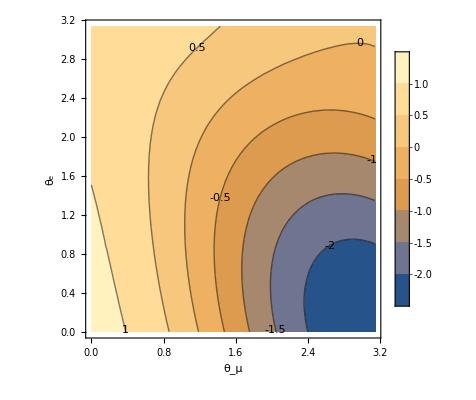

```mathematica
ContourPlot[Tr[Cmatrix/.{Subscript[Ε, 3]->0.998}],{Subscript[θ, 1], 0, π},{Subscript[θ, 2], 0, Pi},PlotLegends->Automatic,ContourLabels->True,PlotLegends->Automatic, 
FrameLabel->{Style["θ_μ",FontSize->14,Blue],Style["θ_e",FontSize->14,Red]}]
```

```mathematica
rho2muThetaNotheta = rho2muTheta
```

(0.0000300176 sin(θ_1)+0.0000391567 sin(1. θ_1)+0.00890016 cos^2(0.5 θ_1)+0.00538095 cos(θ_1)+0.0053812 | 0.178872 sin(θ_1)+0.0625777 cos(θ_1)+0.0638348 | -0.0928715 sin(θ_1)+0.0635337 cos(θ_1)+0.0628787 | 0.0000143323 sin(θ_1)+0.00983118 cos(θ_1)+0.00983104
0.178872 sin(θ_1)+0.0625777 cos(θ_1)+0.0638348 | 2.9392 sin^2(0.5 θ_1)+1.70225 sin(θ_1)+0.594985 sin(1. θ_1)+0.778559 cos^2(0.5 θ_1)-0.961733 cos(θ_1)-0.778559 cos(1. θ_1)+1.81378 | 0.550139 sin(θ_1)+2.11766 cos(θ_1)-1.26561 | 0.17852 sin(θ_1)+0.0635743 cos(θ_1)+0.0628382
-0.0928715 sin(θ_1)+0.0635337 cos(θ_1)+0.0628787 | 0.550139 sin(θ_1)+2.11766 cos(θ_1)-1.26561 | 0.79795 sin^2(0.5 θ_1)-0.886945 sin(θ_1)-0.310013 sin(1. θ_1)+0.778559 cos^2(0.5 θ_1)+0.332865 cos(θ_1)-0.778559 cos(1. θ_1)+0.519186 | -0.0932241 sin(θ_1)+0.0630145 cos(θ_1)+0.063398
0.0000143323 sin(θ_1)+0.00983118 cos(θ_1)+0.00983104 | 0.17852 sin(θ_1)+0.0635743 cos(θ_1)+0.0628382 | -0.0932241 sin(θ_1)+0.0630145 cos(θ_1)+0.063398 | -0.0000300176 sin(θ_1)-0.000010492 sin(1. θ_1)+0.00890016 cos^2(0.5 θ_1)+0.00538095 cos(θ_1)+0.00538104)

```mathematica
rho2Star = KroneckerProduct[PauliMatrix[2], PauliMatrix[2]].rho2muThetaNotheta.KroneckerProduct[PauliMatrix[2], PauliMatrix[2]]
```

(-0.0000300176 sin(θ_1)-0.000010492 sin(1. θ_1)+0.00890016 cos^2(0.5 θ_1)+0.00538095 cos(θ_1)+0.00538104 | 0.0932241 sin(θ_1)-0.0630145 cos(θ_1)-0.063398 | -0.17852 sin(θ_1)-0.0635743 cos(θ_1)-0.0628382 | 0.0000143323 sin(θ_1)+0.00983118 cos(θ_1)+0.00983104
0.0932241 sin(θ_1)-0.0630145 cos(θ_1)-0.063398 | 0.79795 sin^2(0.5 θ_1)-0.886945 sin(θ_1)-0.310013 sin(1. θ_1)+0.778559 cos^2(0.5 θ_1)+0.332865 cos(θ_1)-0.778559 cos(1. θ_1)+0.519186 | 0.550139 sin(θ_1)+2.11766 cos(θ_1)-1.26561 | 0.0928715 sin(θ_1)-0.0635337 cos(θ_1)-0.0628787
-0.17852 sin(θ_1)-0.0635743 cos(θ_1)-0.0628382 | 0.550139 sin(θ_1)+2.11766 cos(θ_1)-1.26561 | 2.9392 sin^2(0.5 θ_1)+1.70225 sin(θ_1)+0.594985 sin(1. θ_1)+0.778559 cos^2(0.5 θ_1)-0.961733 cos(θ_1)-0.778559 cos(1. θ_1)+1.81378 | -0.178872 sin(θ_1)-0.0625777 cos(θ_1)-0.0638348
0.0000143323 sin(θ_1)+0.00983118 cos(θ_1)+0.00983104 | 0.0928715 sin(θ_1)-0.0635337 cos(θ_1)-0.0628787 | -0.178872 sin(θ_1)-0.0625777 cos(θ_1)-0.0638348 | 0.0000300176 sin(θ_1)+0.0000391567 sin(1. θ_1)+0.00890016 cos^2(0.5 θ_1)+0.00538095 cos(θ_1)+0.0053812)

```mathematica
Rmatrix = rho2muThetaNotheta.rho2Star.rho2muThetaNotheta
```

(1)
 |  |  |  |

```mathematica
eivalRmat = Eigenvalues[Rmatrix]
```

{Root[1.10697×10^-13 cos^24(0.5 θ_1)+1.59406×10^-12 sin^2(0.5 θ_1) cos^22(0.5 θ_1)+25824+1.03129×10^-11&,1],Root[1.10697×10^-13 cos^24(0.5 θ_1)+1.59406×10^-12 sin^2(0.5 θ_1) cos^22(0.5 θ_1)+25824+1.03129×10^-11&,2],Root[1.10697×10^-13 cos^24(0.5 θ_1)+1.59406×10^-12 sin^2(0.5 θ_1) cos^22(0.5 θ_1)+25824+1.03129×10^-11&,3],Root[1.10697×10^-13 cos^24(0.5 θ_1)+1.59406×10^-12 sin^2(0.5 θ_1) cos^22(0.5 θ_1)+25824+1.03129×10^-11&,4]}
 |  |  |  |

```mathematica
eivalSum = Table[(eivalRmat[[1]]- eivalRmat[[2]]-eivalRmat[[3]]-eivalRmat[[4]]),{Subscript[θ, 1], 0,0.3, 0.1}]
```

{-4.83726+0. ⅈ,-5.75727+0. ⅈ,-6.58033+0. ⅈ,-7.2216+0. ⅈ}

```mathematica
eivalSum
```

-5.75727+0. ⅈ

```mathematica
Plot[eivalSum,{Subscript[θ, 1], 0, π}]
```

$Aborted

```mathematica
maxVall = Max[0, eivalRmat[[1]]- eivalRmat[[2]]-eivalRmat[[3]]-eivalRmat[[4]]];
```

Max::nord: Invalid comparison with 199.643-48.1639 ⅈ attempted.

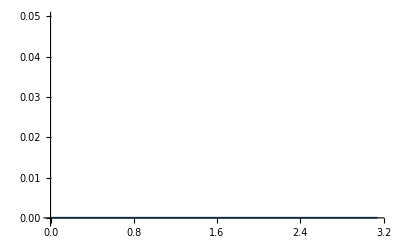

```mathematica
Plot[maxVall,{Subscript[θ, μ], 0, π}, PlotRange->{All,{-0.001, 0.05}}]
```

```mathematica
(*
so C_ij has the following non-zero elements
({{C11, 0, C13}, {0, C22, 0}, {C13, 0, C33}})
*)
```

```mathematica
rdmA[densityMatrix_,dimA_,dimB_ ]:=Table[Tr[Partition[densityMatrix,{dimA,dimB}][[i,j]]],{i,dimA},{j, dimB}]
```

```mathematica
rdmA[rho2muTheta,2,2]
```

(-0.0399172 sin^2(0.5 θ_μ)-0.0824748 sin(θ_μ)-0.225032 sin(1. θ_μ)+43.4357 cos^2(0.5 θ_μ)-68.5447 cos(θ_μ)+21.7378 cos(1. θ_μ)-46.9725 | 3.39182 sin^2(θ_μ/2)+2.84362 sin(θ_μ)+2.61286 cos^2(θ_μ/2)+1.30568 cos(θ_μ)+1.30718
3.39182 sin^2(θ_μ/2)+2.84362 sin(θ_μ)+2.61286 cos^2(θ_μ/2)+1.30568 cos(θ_μ)+1.30718 | 0.0399172 sin^2(0.5 θ_μ)-68.1461 sin(θ_μ)+43.3832 sin(1. θ_μ)+43.4357 cos^2(0.5 θ_μ)-34.2949 cos(θ_μ)+21.6979 cos(1. θ_μ)-81.1823)

```mathematica
partTranspoRho2 =ArrayFlatten[ Table[Partition[rho2muTheta, {2,2}][[i, j]]//Transpose,{i,2},{j,2}]]
```

(-0.0399172 sin^2(0.5 θ_μ)-0.217977 sin(θ_μ)-0.138769 sin(1. θ_μ)-0.316188 cos(θ_μ)+0.0199586 cos(1. θ_μ)-0.46155 | -0.00672282 sin^2(θ_μ/2)-0.00714012 sin(θ_μ)+2.61286 cos^2(θ_μ/2) | 3.39182 sin^2(θ_μ/2)+3.60235 sin(θ_μ)+2.61286 cos^2(θ_μ/2) | 0.135772 sin^2(θ_μ/2)-12.3965 sin(θ_μ)-49.5859 cos^2(θ_μ/2)
-0.00672282 sin^2(θ_μ/2)-0.00714012 sin(θ_μ)+2.61286 cos^2(θ_μ/2) | 0.135502 sin(θ_μ)-0.0862636 sin(1. θ_μ)+43.4357 cos^2(0.5 θ_μ)-68.2285 cos(θ_μ)+21.7178 cos(1. θ_μ)-46.5109 | -0.138769 sin(θ_μ)-0.37889 cos(θ_μ)-0.37889 | -0.758736 sin(θ_μ)+1.30568 cos(θ_μ)+1.30718
3.39182 sin^2(θ_μ/2)+3.60235 sin(θ_μ)+2.61286 cos^2(θ_μ/2) | -0.138769 sin(θ_μ)-0.37889 cos(θ_μ)-0.37889 | -68.3641 sin(θ_μ)+43.5219 sin(1. θ_μ)+43.4357 cos^2(0.5 θ_μ)-33.9787 cos(θ_μ)+21.7178 cos(1. θ_μ)-80.7607 | 2.85076 sin(θ_μ)+1.68297 cos(θ_μ)+0.929885
0.135772 sin^2(θ_μ/2)-12.3965 sin(θ_μ)-49.5859 cos^2(θ_μ/2) | -0.758736 sin(θ_μ)+1.30568 cos(θ_μ)+1.30718 | 2.85076 sin(θ_μ)+1.68297 cos(θ_μ)+0.929885 | 0.0399172 sin^2(0.5 θ_μ)+0.217977 sin(θ_μ)-0.138769 sin(1. θ_μ)-0.316188 cos(θ_μ)-0.0199586 cos(1. θ_μ)-0.421633)

```mathematica
Dimensions[partTranspoRho2]
```

{4,4}

```mathematica
eigenVals = Eigenvalues[partTranspoRho2];
```

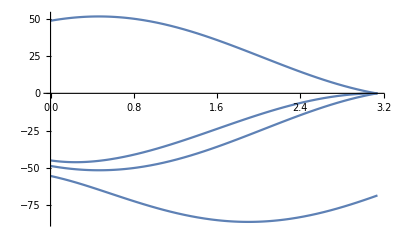

```mathematica
Plot[Table[eigenVals[[i]],{i, 4}],{Subscript[θ, μ], 0, π}]
```

```mathematica
nrho = 1/2 Sum[Abs[eigenVals[[i]]]-eigenVals[[i]],{i, 4}];
```

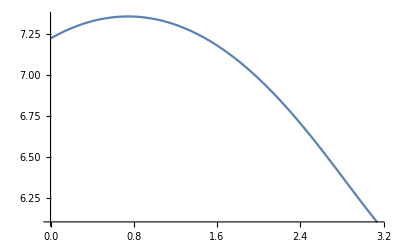

```mathematica
Plot[Log[2, nrho],{Subscript[θ, μ], 0, π}]
```

```mathematica
-Sum[eigenVals[[i]]*Log[eigenVals[[i]]],{i, 4}]
```

-log(Root[-4.63883×10^6 cos^4(θ_μ/2) cos^4(0.5 θ_μ)-3.00616 sin^4(0.5 θ_μ) cos^4(0.5 θ_μ)-34.7785 sin^4(θ_μ/2) cos^4(0.5 θ_μ)+483+77.4566 sin(1. θ_μ)+(1193.08 cos(θ_μ) cos^4(0.5 θ_μ)+523.618 sin(1. θ_μ) cos^4(0.5 θ_μ)+1666.26 cos^4(0.5 θ_μ)+214189. cos^4(θ_μ/2) cos^2(0.5 θ_μ)+0.138419 sin^4(0.5 θ_μ) cos^2(0.5 θ_μ)+501.306 sin^4(θ_μ/2) cos^2(0.5 θ_μ)-2619. cos^2(θ_μ) cos^2(0.5 θ_μ)+146+53393. cos^2(θ_μ/2) sin(θ_μ) sin(1. θ_μ)+0.755871 sin^2(0.5 θ_μ) sin(θ_μ) sin(1. θ_μ)-151.707 sin^2(θ_μ/2) sin(θ_μ) sin(1. θ_μ)+1218.56 cos(θ_μ) sin(θ_μ) sin(1. θ_μ)-411.627 cos(1. θ_μ) sin(θ_μ) sin(1. θ_μ)+811.321 sin(θ_μ) sin(1. θ_μ)-658.085 sin(1. θ_μ)+3163.62) #1+649.127&,1]) Root[1&,1]-1-1-log(Root[1&,4]) Root[1]
 |  |  |  |